# EulerizeGraph

Add edges to a graph to make it Eulerian

## Definition

```mathematica
ClearAll[EulerizeGraph]
EulerizeGraph[graph_?ConnectedGraphQ]:=NestWhile[(x↦EdgeAdd[x,UndirectedEdge[First[#],Last[#]]&@First@TakeDrop[Select[VertexList[x],OddQ[VertexDegree[x,#]]&],2]]),graph,!EulerianGraphQ[#]&]
```

## Documentation

### Usage

EulerizeGraph[graph]

adds edges to a connected graph to make it Eulerian.

### Details & Options

A Eulerian graph is also referred to as unicursal.

A graph is Eulerian if it contains a path through all edges with no repetitions.

If the input graph is already Eulerian it is returned unchanged.

## Examples

### Basic Examples

Create the bridges of Königsberg graph:

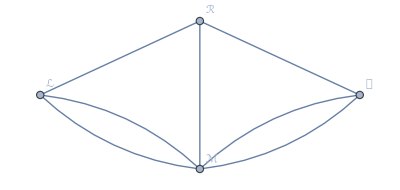

```mathematica
islands={𝒯,ℒ,ℳ,ℛ};
bridges={ℒ<->ℳ,ℒ<->ℳ,𝒯<->ℳ,𝒯<->ℳ,ℳ<->ℛ,ℛ<->𝒯,ℛ<->ℒ};
bridgesOfKonigsbergSystem=Graph[islands,bridges,VertexLabels->"Name"]
```

Eulerize the Königsberg graph:

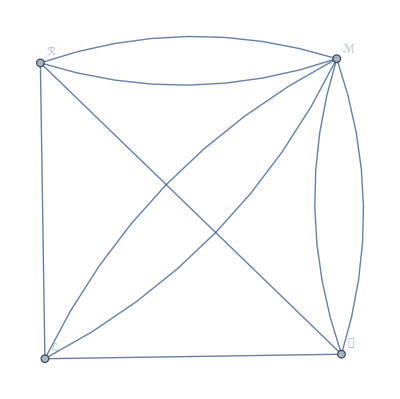

```mathematica
EulerizeGraph[bridgesOfKonigsbergSystem]
```

Eulerize the graph corresponding to the modern-day bridges of Königsberg (some of the original bridges are no longer present):

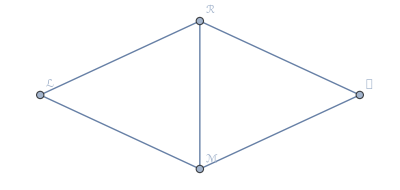
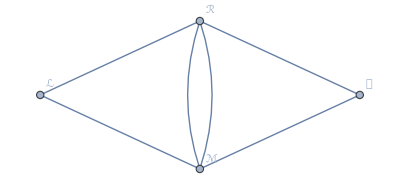

```mathematica
Konigsburg2022=Graph[islands,{ℒ<->ℛ,ℛ<->ℳ,𝒯<->ℳ,ℳ<->ℒ,ℛ<->𝒯},VertexLabels->"Name"];
Row[{Konigsburg2022,EulerizeGraph[Konigsburg2022]}]
```

Show the Pappus graph and its Eulerized counterpart:

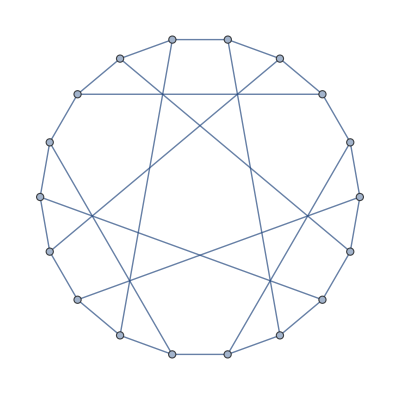
-Graphics--Graphics-

```mathematica
pappusgraph=GraphData["PappusGraph"];
Row[{pappusgraph,EulerizeGraph[pappusgraph]}]
```

### Properties and Relations

If a graph is already Eulerian, the graph remains unchanged:

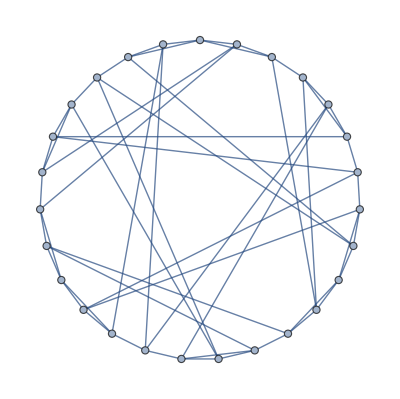

```mathematica
pappusLineGraph=GraphData["PappusLineGraph"]
```

Check that it is Eulerian:

```mathematica
EulerianGraphQ[pappusLineGraph]
```

True

Check that the original and Eulerized graphs are identical:

```mathematica
pappusLineGraph===EulerizeGraph[pappusLineGraph]
```

True

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

Graph Theory

Eulerian Path

Chinese Postman Problem

Arc Routing Problems

Fleury's Algorithm

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

EulerianGraphQ

FindEulerianCycle

FindPostmanTour

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.